16.5174-20.4626 ⅈ

16.5174-20.4626 ⅈ

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

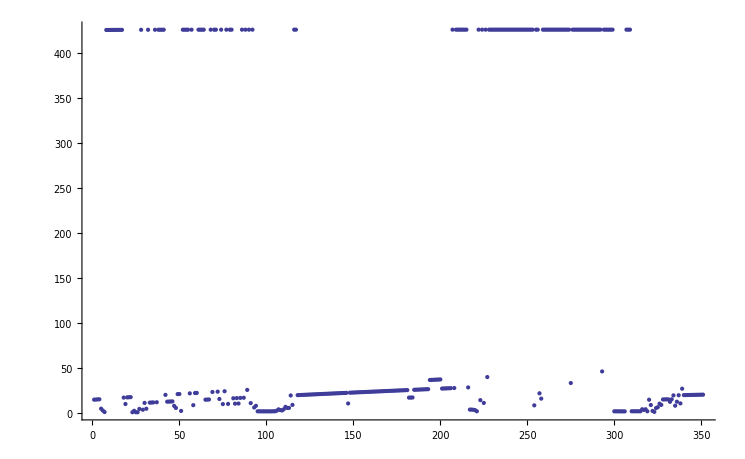

res_s.txt

res_a.txt

-Graphics3D-

```mathematica
(* Clear all data before calculations *)
Clear[r, x, r12, r21, r34, r43, z, r13, r31, r24, r42, diag, r14, r41, r23, r32, clight, ωp, fp, γ, sol, M];

(* Length of nanorods *)
x = 100;
r12 = x;
r21 = x;
r34 = x;
r43 = x;

(* Distance btw nanorods *)
z = 30;
r = z;

(* Constants [nm/fs] *)
clight = 300;
fp =2.183;  (* plasma frequency of gold in 1/fs *)
ωp = 2π fp;
a = 10;
γ =0 *6.46*10^(-3);


(* Drude model & phys functions *)
ϵ[ω_] := 7.397- 4.663/(ω^2+ ⅈ γ ω);
α[ω_] := (ϵ[ω] - 1)/(ϵ[ω]+2) * a^3; 
k[ω_] :=ω/clight ;

(* Define tensor components *)

χ[ω_] := Exp[ⅈ k[ω] r] /r * (k[ω]^2 + ⅈ k[ω] /r - 1/r^2);

(* Finding resonance frequencies *)

FindRoot[1/α[ω] - χ[ω] == 0, {ω, 9}][[1]][[2]]
FindRoot[χ[ω] - 1/α[ω] == 0, {ω, 9}][[1]][[2]]

(* Symmetrical mode *)
Clear[ω, sol1, w, z, listYs, listX, lambda];
a = 10;
listX = {};
listYs = {};
Do[z = i;
r = z;
AppendTo[listX, N[z]];
sol1 = FindRoot[χ[ω] - 1/α[ω] == 0, {ω, 9}][[1]][[2]];;
w = Abs[sol1];
lambda = clight/ w;
AppendTo[listYs, lambda], {i, 50,400, 1}];
ListPlot[{listYs}, PlotRange -> All]

(* Antisymmetrical mode *)
(* Clear[ω, sol2, w, z, listYa, listX, a];
a = 1;
listX = {};
listYa = {};
Do[z = i;
r = z;
AppendTo[listX, N[z]];
sol2 = FindRoot[χ[ω] + 1/α[ω] == 0, {ω, 9}][[1]][[2]];;
w = Abs[sol2];
AppendTo[listYa, w], {i, 30,400, 1}];
ListPlot[{listYs, listYa}, PlotRange -> All]

(* Exporting data *)
Export["res_s.txt",listYs,"Table"]
Export["res_a.txt",listYa,"Table"]

(* 3D plot "a" vary *)
Clear[ω, sol, w, z, listY, listYtemp, a];
a = 1;
listY = {};
Do[ a =j;
Clear[listYtemp];
listYtemp = {};
Do[z = i;
r = z;
sol = FindRoot[χ[ω] - 1/α[ω] == 0, {ω, 2}][[1]][[2]];;
w = Abs[sol];
AppendTo[listYtemp, w], {i, 30,400, 1}];
AppendTo[listY, listYtemp], {j, 1, 2, 0.1}];
ListPlot3D[listY, PlotRange -> All] *)
```